Inserisco la matrice del sistema tempo discreto

```mathematica
A={{1/8,1/8},{-13/8,3/8}}
```

{{1/8,1/8},{-13/8,3/8}}

calcolo il polinomio caratteristico di A e i suoi autovalori

```mathematica
CharacteristicPolynomial[A,λ]
```

1/4-λ/2+λ^2

```mathematica
λ=Eigenvalues[A]
```

{1/4 (1+ⅈ √3),1/4 (1-ⅈ √3)}

Mi calcolo modulo e argomento del primo autovalore (l’ho scelto io)

```mathematica
ρ=Abs[λ[[1]]]
```

1/2

```mathematica
θ=Arg[λ[[1]]]
```

π/3

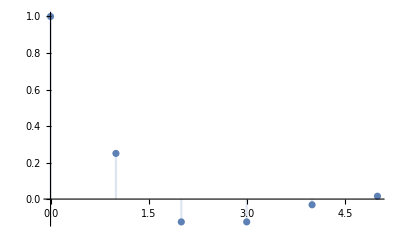

```mathematica
DiscretePlot[ρ^k Cos[θ k],{k,0,5}]
```

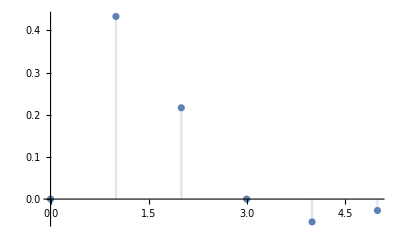

```mathematica
DiscretePlot[ρ^k Sin[θ k],{k,0,5}]
```

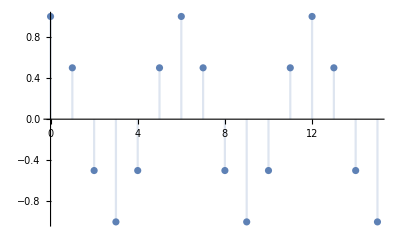

```mathematica
DiscretePlot[Cos[θ k],{k,0,15}]
```